```mathematica
initialSeedPoly[exp_,x_]:=Expand[exp/.{x->(x-Coefficient[exp,x^(Exponent[exp,x]-1)]/Exponent[exp,x])}];
stageTwoSeedPoly[exp_,x_]:=Expand[x^Exponent[exp,x]+Sum[-Abs[Coefficient[exp,x^i]]x^i,{i,1,Exponent[exp,x]-2}]-Abs[exp-Sum[Coefficient[exp,x^i]x^i,{i,1,Exponent[exp,x]}]]];
initialSeed[exp_,x_]:=
Do[
Clear[n,z,exp1,i,c1,flag];
i=0;
n =Exponent[exp,x];
c1=Coefficient[exp,x^(n-1)];
exp1=stageTwoSeedPoly[initialSeedPoly[exp,x],x];
While[
Not[And[(exp1/.x->i)≤0,(exp1/.x->i+1)≥0]],
i=i+1;
];
Return[Table[-c1/n+Round[i+1]Exp[I*(2Pi/n*(k-1)+Pi/2/n)],{k,1,n}]];
,1];
PACARootFinder[exp_,x_]:=If[
Exponent[exp,x]==1,
-(exp-x Coefficient[exp,x])/Coefficient[exp,x],
Do[
Clear[n1,z,z1,i,flag];
n1=Exponent[exp,x];
z =N[initialSeed[exp,x]];
While[True,
z1 = Table[z[[i]]+(exp/.x->z[[i]])/((exp/.x->z[[i]])*Sum[If[k≠i,1/(z[[i]]-z[[k]]),0],{k,1,n1}]-(D[exp,x]/.x->z[[i]])),{i,1,n1}];
flag=True;
For[i=1,i≤n1,i++,flag=And[flag,Abs[z[[i]]-z1[[i]]]<10^(-5)]];
If[flag,Break[]];
For[i=1,i≤n1,i++,z[[i]]=z1[[i]]];
];
Return[z1];
,1]];
NewPACARootFinder[exp_,x_]:=
Do[
Clear[n,cp,exp1,exp2,c0,exp3];
n=Exponent[exp,x];
cp=Coefficient[exp,x^n];
exp1=SetPrecision[N[Expand[exp/cp]],2];
c0=exp1/.x->0;
(*Refining the coefficients*)
exp2=If[Abs[c0]<0.001,Sign[Re[c0]]0.001+I Sign[Im[c0]]0.001,c0]+Sum[ If[Abs[Coefficient[exp1,x^i]]<0.001,Sign[Re[Coefficient[exp1,x^i]]]0.001+I Sign[Im[Coefficient[exp1,x^i]]]0.001,Coefficient[exp1,x^i] ]*x^i,{i,1,n}];
cp=Coefficient[exp2,x^n];
exp3=SetPrecision[N[Expand[exp2/cp]],2];
Return[PACARootFinder[exp3,x]]
,1];
```

```mathematica
initialSeed[x^5-10x^4+43x^3-104x^2+150x-100,x]
```

{2+3 ⅇ^((ⅈ π)/10),2+3 ⅈ,2+3 ⅇ^((9 ⅈ π)/10),2+3 ⅇ^(-(7 ⅈ π)/10),2+3 ⅇ^(-(3 ⅈ π)/10)}

```mathematica
PACARootFinder[x^5-10x^4+43x^3-104x^2+150x-100,x]
```

{3.+1. ⅈ,1.+2. ⅈ,2.+1.07285×10^-28 ⅈ,1.-2. ⅈ,3.-1. ⅈ}

```mathematica
initialSeed[x^2+2 x + 1,x]
```

{-1+ⅇ^((ⅈ π)/4),-1+ⅇ^(-(3 ⅈ π)/4)}

```mathematica
NewPACARootFinder[x^2-2 x + 1,x]
```

{1.+1.33055×10^-6 ⅈ,0.999999-1.33055×10^-6 ⅈ}

```mathematica
NSolve[x^5-10x^4+43x^3-104x^2+150x-100==0,x]
```

{{x→1.-2. ⅈ},{x→1.+2. ⅈ},{x→2.},{x→3.-1. ⅈ},{x→3.+1. ⅈ}}

```mathematica
Start=AbsoluteTime[];
PACARootFinder[x^7-1,x]
end=AbsoluteTime[];
Print[end-Start]
```

{1.+0. ⅈ,0.62349+0.781831 ⅈ,-0.222521+0.974928 ⅈ,-0.900969+0.433884 ⅈ,-0.900969-0.433884 ⅈ,-0.222521-0.974928 ⅈ,0.62349-0.781831 ⅈ}

0.

```mathematica
Start=AbsoluteTime[];
NSolve[x^7-1==0,x]
end=AbsoluteTime[];
Print[end-Start]
```

{{x→-0.900969-0.433884 ⅈ},{x→-0.900969+0.433884 ⅈ},{x→-0.222521-0.974928 ⅈ},{x→-0.222521+0.974928 ⅈ},{x→0.62349-0.781831 ⅈ},{x→0.62349+0.781831 ⅈ},{x→1.}}

0.019006

```mathematica
xp[exp_,x_]:=Do[
Clear[exp1,n,slnroot,i,m];
exp1=Numerator[Together[exp]];
n=Exponent[exp1,x];
slnroot = NewPACARootFinder[exp1,x];
m = 0;
For[i=1,i≤n,i++,
r=Re[slnroot[[i]]];
im=Abs[Im[slnroot[[i]]]];
If[im<10^(-3)&&m<r,m =r];
];
Return[m]
,1];
aExpression[n_,exp_,x_,W_,ω_]:=
Do[
Clear[R,S,T,U,k,root,dexp,p,q,r];
root =xp[exp,x];
dexp=D[exp,x];
R=Table[1,{k,1,n+1}];
S=N[CoefficientList[Series[x^4 exp,{x,root,n}],x]];
T=N[CoefficientList[Series[(x-root)(2x^3exp+x^4dexp+2I ω x),{x,root,n}],x]];
U=N[CoefficientList[Series[-(x-root)^2(W(W+1)x^2-x^3dexp),{x,root,n}],x]];
q=S[[1]];r=T[[1]];
For[k=2,k≤n+1,k++,
p=-1/(k*(k-1)q+k r );
R[[k]]=Simplify[p Sum[(l(l-1)S[[k-l+1]]+l T[[k-l+1]]+U[[k-l+1]])R[[l]],{l,1,k-1}]
]];
Return[R]
,1];
PACAGetModes[m_,exp_,x_,W_]:=
Do[
Clear[exp1,CoeffList,ω,exp1,s,r,root];
CoeffList=aExpression[m,exp,x,W,ω];
root=xp[exp,x];
exp1=Sum[CoeffList[[n]](-root)^(n-1),{n,1,m+1}];
s=Numerator[Together[exp1]];
r=NewPACARootFinder[s,ω];
Return[r]
,1];
```

```mathematica
N[CoefficientList[Series[Sin[x],{x,0,30}],x]]
```

{0.,1.,0.,-0.166667,0.,0.00833333,0.,-0.000198413,0.,2.75573×10^-6,0.,-2.50521×10^-8,0.,1.6059×10^-10,0.,-7.64716×10^-13,0.,2.81146×10^-15,0.,-8.22064×10^-18,0.,1.95729×10^-20,0.,-3.86817×10^-23,0.,6.44695×10^-26,0.,-9.18369×10^-29,0.,1.131×10^-31}

```mathematica
xp[(1-2 M x+Q^2x^2)/.{M->7,Q->3},x]
```

1.48051

```mathematica
PACAGetModes[6,(1-2 M x+Q^2x^2)/.{M->7,Q->3},x,0]
```

{0.3127+0.0155939 ⅈ,0.146779+0.265924 ⅈ,-0.146779+0.265924 ⅈ,-0.3127+0.0155939 ⅈ,-0.177774-0.281018 ⅈ,0.177774-0.281018 ⅈ}

```mathematica
PACAGetModes[3,(1-2 M x+Q^2x^2+1/x^2/l^2)/.{M->7,Q->3,l->9},x,0]
```

{-726.142-1391.03 ⅈ,726.142-1391.03 ⅈ,0.-325.877 ⅈ}

```mathematica
PACAGetModes[6,(1-2 M x+Q^2x^2+1/x^2/l^2)/.{M->7,Q->3,l->9},x,0]
```

{0.31168-0.0252975 ⅈ,0.17693+0.271074 ⅈ,-0.17693+0.271074 ⅈ,-0.31168-0.0252975 ⅈ,-0.14631-0.276023 ⅈ,0.14631-0.276023 ⅈ}

```mathematica
PACAGetModes[15,(1-2 M x+Q^2x^2+1/x^2/l^2)/.{M->7,Q->3,l->9},x,0]
```

{0.623699+0.0360952 ⅈ,0.563473+0.287318 ⅈ,0.405549+0.502519 ⅈ,0.158305+0.648229 ⅈ,-0.158305+0.648229 ⅈ,-0.405549+0.502519 ⅈ,-0.563473+0.287318 ⅈ,-0.623699+0.0360952 ⅈ,-0.582232-0.214061 ⅈ,-0.447981-0.425726 ⅈ,-0.243071-0.567027 ⅈ,2.75506×10^-40-0.616628 ⅈ,0.243071-0.567027 ⅈ,0.447981-0.425726 ⅈ,0.582232-0.214061 ⅈ}

```mathematica
PACAPlotModes[m_,exp_,x_,W_]:=ListPlot[(Tooltip[{Re[#1],Abs[Im[#1]]}]&)/@PACAGetModes[m,exp,x,W],AspectRatio->1,AxesLabel->{ωR,ωI}];
```

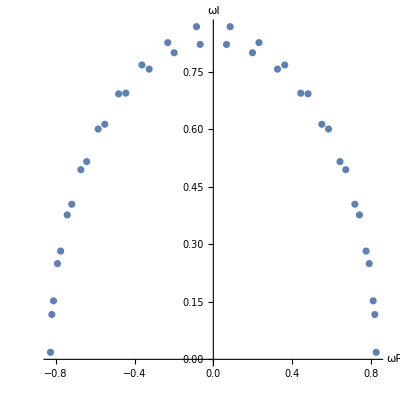

```mathematica
PACAPlotModes[38,(1-2 M x+Q^2x^2+1/x^2/l^2)/.{M->15,Q->9,l->8},x,1]
```